```mathematica
Quit[]
```

### Geometry

```mathematica
n=4
```

4

```mathematica
coord={r,θ,ϕ,t}
```

{r,θ,ϕ,t}

```mathematica
metric={{A[r,t]^2,0,0,0},{0,B[r,t]^2 r^2,0,0},{0,0,B[r,t]^2 r^2 Sin[θ]^2,0},{0,0,0,-1}}
```

{{A[r,t]^2,0,0,0},{0,r^2 B[r,t]^2,0,0},{0,0,r^2 B[r,t]^2 Sin[θ]^2,0},{0,0,0,-1}}

```mathematica
metric//MatrixForm
```

(A[r,t]^2 | 0 | 0 | 0
0 | r^2 B[r,t]^2 | 0 | 0
0 | 0 | r^2 B[r,t]^2 Sin[θ]^2 | 0
0 | 0 | 0 | -1)

```mathematica
Det[metric]
```

-r^4 A[r,t]^2 B[r,t]^4 Sin[θ]^2

```mathematica
inversemetric=Simplify[Inverse[metric]]
```

{{1/A[r,t]^2,0,0,0},{0,1/(r^2 B[r,t]^2),0,0},{0,0,Csc[θ]^2/(r^2 B[r,t]^2),0},{0,0,0,-1}}

```mathematica
inversemetric//MatrixForm
```

(1/A[r,t]^2 | 0 | 0 | 0
0 | 1/(r^2 B[r,t]^2) | 0 | 0
0 | 0 | Csc[θ]^2/(r^2 B[r,t]^2) | 0
0 | 0 | 0 | -1)

```mathematica
affine:=affine=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*(D[metric[[s,j]],coord[[k]]]+D[metric[[s,k]],coord[[j]]]-D[metric[[j,k]],coord[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}]]
```

```mathematica
listaffine:=Table[If[UnsameQ[affine[[i,j,k]],0],{ToString[Γ[i,j,k]],affine[[i,j,k]]}],{i,1,n},{j,1,n},{k,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listaffine],Null],2],TableSpacing->{2,2}]
```

Γ[1, 1, 1] | (A^(1,0)[r,t])/A[r,t]
Γ[1, 2, 2] | -(r B[r,t] (B[r,t]+r B^(1,0)[r,t]))/A[r,t]^2
Γ[1, 3, 3] | -(r B[r,t] Sin[θ]^2 (B[r,t]+r B^(1,0)[r,t]))/A[r,t]^2
Γ[1, 4, 1] | (A^(0,1)[r,t])/A[r,t]
Γ[2, 2, 1] | 1/r+(B^(1,0)[r,t])/B[r,t]
Γ[2, 3, 3] | -Cos[θ] Sin[θ]
Γ[2, 4, 2] | (B^(0,1)[r,t])/B[r,t]
Γ[3, 3, 1] | 1/r+(B^(1,0)[r,t])/B[r,t]
Γ[3, 3, 2] | Cot[θ]
Γ[3, 4, 3] | (B^(0,1)[r,t])/B[r,t]
Γ[4, 1, 1] | A[r,t] A^(0,1)[r,t]
Γ[4, 2, 2] | r^2 B[r,t] B^(0,1)[r,t]
Γ[4, 3, 3] | r^2 B[r,t] Sin[θ]^2 B^(0,1)[r,t]

```mathematica
riemann:=riemann=Simplify[Table[D[affine[[i,j,l]],coord[[k]]]-D[affine[[i,j,k]],coord[[l]]]+Sum[affine[[s,j,l]]affine[[i,k,s]]-affine[[s,j,k]]affine[[i,l,s]],{s,1,n}],{i,1,n},{j,1,n},{k,1,n},{l,1,n}]]
```

```mathematica
listriemann:=Table[If[UnsameQ[riemann[[i,j,k,l]],0],{ToString[R[i,j,k,l]],riemann[[i,j,k,l]]}],{i,1,n},{j,1,n},{k,1,n},{l,1,k-1}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listriemann],Null],2],TableSpacing->{2,2}]
```

R[1, 2, 2, 1] | -(r B[r,t] (r A[r,t]^2 A^(0,1)[r,t] B^(0,1)[r,t]+A^(1,0)[r,t] (B[r,t]+r B^(1,0)[r,t])-A[r,t] (2 B^(1,0)[r,t]+r B^(2,0)[r,t])))/A[r,t]^3
R[1, 2, 4, 2] | (r B[r,t] (B[r,t] A^(0,1)[r,t]+r A^(0,1)[r,t] B^(1,0)[r,t]-A[r,t] (B^(0,1)[r,t]+r B^(1,1)[r,t])))/A[r,t]^3
R[1, 3, 3, 1] | -(r B[r,t] Sin[θ]^2 (r A[r,t]^2 A^(0,1)[r,t] B^(0,1)[r,t]+A^(1,0)[r,t] (B[r,t]+r B^(1,0)[r,t])-A[r,t] (2 B^(1,0)[r,t]+r B^(2,0)[r,t])))/A[r,t]^3
R[1, 3, 4, 3] | (r B[r,t] Sin[θ]^2 (B[r,t] A^(0,1)[r,t]+r A^(0,1)[r,t] B^(1,0)[r,t]-A[r,t] (B^(0,1)[r,t]+r B^(1,1)[r,t])))/A[r,t]^3
R[1, 4, 4, 1] | (A^(0,2)[r,t])/A[r,t]
R[2, 1, 2, 1] | (r A[r,t]^2 A^(0,1)[r,t] B^(0,1)[r,t]+A^(1,0)[r,t] (B[r,t]+r B^(1,0)[r,t])-A[r,t] (2 B^(1,0)[r,t]+r B^(2,0)[r,t]))/(r A[r,t] B[r,t])
R[2, 1, 4, 2] | (-B[r,t] A^(0,1)[r,t]-r A^(0,1)[r,t] B^(1,0)[r,t]+A[r,t] (B^(0,1)[r,t]+r B^(1,1)[r,t]))/(r A[r,t] B[r,t])
R[2, 3, 3, 2] | Sin[θ]^2 (-1-r^2 (B^(0,1)[r,t])^2+((B[r,t]+r B^(1,0)[r,t])^2)/A[r,t]^2)
R[2, 4, 2, 1] | (B[r,t] A^(0,1)[r,t]+r A^(0,1)[r,t] B^(1,0)[r,t]-A[r,t] (B^(0,1)[r,t]+r B^(1,1)[r,t]))/(r A[r,t] B[r,t])
R[2, 4, 4, 2] | (B^(0,2)[r,t])/B[r,t]
R[3, 1, 3, 1] | (r A[r,t]^2 A^(0,1)[r,t] B^(0,1)[r,t]+A^(1,0)[r,t] (B[r,t]+r B^(1,0)[r,t])-A[r,t] (2 B^(1,0)[r,t]+r B^(2,0)[r,t]))/(r A[r,t] B[r,t])
R[3, 1, 4, 3] | (-B[r,t] A^(0,1)[r,t]-r A^(0,1)[r,t] B^(1,0)[r,t]+A[r,t] (B^(0,1)[r,t]+r B^(1,1)[r,t]))/(r A[r,t] B[r,t])
R[3, 2, 3, 2] | 1+r^2 (B^(0,1)[r,t])^2-((B[r,t]+r B^(1,0)[r,t])^2)/A[r,t]^2
R[3, 4, 3, 1] | (B[r,t] A^(0,1)[r,t]+r A^(0,1)[r,t] B^(1,0)[r,t]-A[r,t] (B^(0,1)[r,t]+r B^(1,1)[r,t]))/(r A[r,t] B[r,t])
R[3, 4, 4, 3] | (B^(0,2)[r,t])/B[r,t]
R[4, 1, 4, 1] | A[r,t] A^(0,2)[r,t]
R[4, 2, 2, 1] | (r B[r,t] (B[r,t] A^(0,1)[r,t]+r A^(0,1)[r,t] B^(1,0)[r,t]-A[r,t] (B^(0,1)[r,t]+r B^(1,1)[r,t])))/A[r,t]
R[4, 2, 4, 2] | r^2 B[r,t] B^(0,2)[r,t]
R[4, 3, 3, 1] | (r B[r,t] Sin[θ]^2 (B[r,t] A^(0,1)[r,t]+r A^(0,1)[r,t] B^(1,0)[r,t]-A[r,t] (B^(0,1)[r,t]+r B^(1,1)[r,t])))/A[r,t]
R[4, 3, 4, 3] | r^2 B[r,t] Sin[θ]^2 B^(0,2)[r,t]

```mathematica
ricci:=ricci=Simplify[Table[Sum[riemann[[i,j,i,l]],{i,1,n}],{j,1,n},{l,1,n}]]
```

```mathematica
listricci:=Table[If[UnsameQ[ricci[[j,l]],0],{ToString[R[j,l]],ricci[[j,l]]}],{j,1,n},{l,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listricci],Null],2],TableSpacing->{2,2}]
```

R[1, 1] | A[r,t] A^(0,2)[r,t]+(2 (r A[r,t]^2 A^(0,1)[r,t] B^(0,1)[r,t]+A^(1,0)[r,t] (B[r,t]+r B^(1,0)[r,t])-A[r,t] (2 B^(1,0)[r,t]+r B^(2,0)[r,t])))/(r A[r,t] B[r,t])
R[2, 2] | 1+r^2 (B^(0,1)[r,t])^2+r^2 B[r,t] B^(0,2)[r,t]-((B[r,t]+r B^(1,0)[r,t])^2)/A[r,t]^2+(r B[r,t] (r A[r,t]^2 A^(0,1)[r,t] B^(0,1)[r,t]+A^(1,0)[r,t] (B[r,t]+r B^(1,0)[r,t])-A[r,t] (2 B^(1,0)[r,t]+r B^(2,0)[r,t])))/A[r,t]^3
R[3, 3] | Sin[θ]^2 (1+r^2 (B^(0,1)[r,t])^2+r^2 B[r,t] B^(0,2)[r,t]-((B[r,t]+r B^(1,0)[r,t])^2)/A[r,t]^2+(r B[r,t] (r A[r,t]^2 A^(0,1)[r,t] B^(0,1)[r,t]+A^(1,0)[r,t] (B[r,t]+r B^(1,0)[r,t])-A[r,t] (2 B^(1,0)[r,t]+r B^(2,0)[r,t])))/A[r,t]^3)
R[4, 1] | (2 (B[r,t] A^(0,1)[r,t]+r A^(0,1)[r,t] B^(1,0)[r,t]-A[r,t] (B^(0,1)[r,t]+r B^(1,1)[r,t])))/(r A[r,t] B[r,t])
R[4, 4] | -(A^(0,2)[r,t])/A[r,t]-(2 B^(0,2)[r,t])/B[r,t]

```mathematica
scalar=Simplify[Sum[inversemetric[[i,j]]ricci[[i,j]],{i,1,n},{j,1,n}]]
```

1/(r^2 A[r,t]^3 B[r,t]^2)2 (r^2 A[r,t]^2 B[r,t] (2 A^(0,1)[r,t] B^(0,1)[r,t]+B[r,t] A^(0,2)[r,t])+A[r,t]^3 (1+r^2 (B^(0,1)[r,t])^2+2 r^2 B[r,t] B^(0,2)[r,t])+2 r B[r,t] A^(1,0)[r,t] (B[r,t]+r B^(1,0)[r,t])-A[r,t] (B[r,t]^2+r^2 (B^(1,0)[r,t])^2+2 r B[r,t] (3 B^(1,0)[r,t]+r B^(2,0)[r,t])))

```mathematica
einstein:=einstein=Simplify[ricci-(1/2)scalar*metric]
```

```mathematica
listeinstein:=Table[If[UnsameQ[einstein[[j,l]],0],{ToString[G[j,l]],einstein[[j,l]]}],{j,1,n},{l,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listeinstein],Null],2],TableSpacing->{2,2}]
```

G[1, 1] | (-A[r,t]^2 (1+r^2 (B^(0,1)[r,t])^2+2 r^2 B[r,t] B^(0,2)[r,t])+(B[r,t]+r B^(1,0)[r,t])^2)/(r^2 B[r,t]^2)
G[2, 2] | -(r B[r,t] (r A[r,t]^2 (A^(0,1)[r,t] B^(0,1)[r,t]+B[r,t] A^(0,2)[r,t])+r A[r,t]^3 B^(0,2)[r,t]+A^(1,0)[r,t] (B[r,t]+r B^(1,0)[r,t])-A[r,t] (2 B^(1,0)[r,t]+r B^(2,0)[r,t])))/A[r,t]^3
G[3, 3] | -(r B[r,t] Sin[θ]^2 (r A[r,t]^2 (A^(0,1)[r,t] B^(0,1)[r,t]+B[r,t] A^(0,2)[r,t])+r A[r,t]^3 B^(0,2)[r,t]+A^(1,0)[r,t] (B[r,t]+r B^(1,0)[r,t])-A[r,t] (2 B^(1,0)[r,t]+r B^(2,0)[r,t])))/A[r,t]^3
G[4, 1] | (2 (B[r,t] A^(0,1)[r,t]+r A^(0,1)[r,t] B^(1,0)[r,t]-A[r,t] (B^(0,1)[r,t]+r B^(1,1)[r,t])))/(r A[r,t] B[r,t])
G[4, 4] | (2 r^2 A[r,t]^2 B[r,t] A^(0,1)[r,t] B^(0,1)[r,t]+A[r,t]^3 (1+r^2 (B^(0,1)[r,t])^2)+2 r B[r,t] A^(1,0)[r,t] (B[r,t]+r B^(1,0)[r,t])-A[r,t] (B[r,t]^2+r^2 (B^(1,0)[r,t])^2+2 r B[r,t] (3 B^(1,0)[r,t]+r B^(2,0)[r,t])))/(r^2 A[r,t]^3 B[r,t]^2)

### Static

```mathematica
StaticEoM={-f''[x]-2/x f'[x]+(2f[x])/x^2+f[x](f[x]^2-1)==0};
```

```mathematica
xi=10^-4;
xf=25;
insl=0.50604324925;
```

```mathematica
BC={f[xi]==xi insl,f'[xi]==insl};
```

```mathematica
StaticSol=NDSolve[Join[StaticEoM,BC],f[x],{x,xi,xf},PrecisionGoal->16][[1]];
```

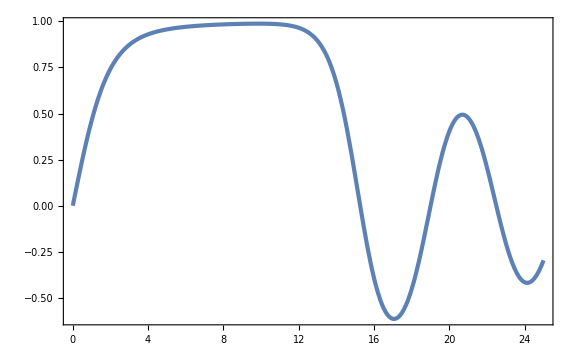

```mathematica
Plot[f[x]/.StaticSol,{x,xi,xf},PlotRange->Full]
```

```mathematica
xmax=10;
tab=Table[{x,f[x]/.StaticSol},{x,xi,xmax,(xmax-xi)/100}];
fit=FindFit[tab,a Tanh[b x]+c Tanh[d x]^2,{a,b,c,d},x]
```

{a→0.890808,b→0.563644,c→0.100134,d→0.250617}

```mathematica
fsol[x_]=a Tanh[b x]+c Tanh[d x]^2/.fit
```

0.100134 Tanh[0.250617 x]^2+0.890808 Tanh[0.563644 x]

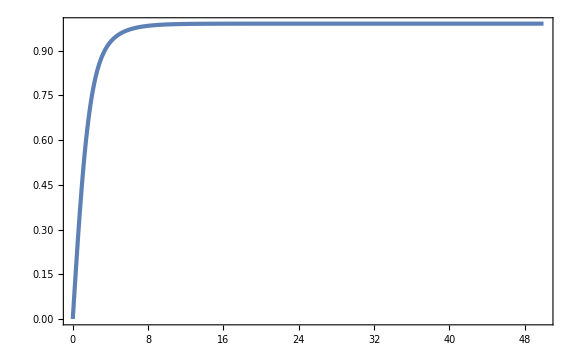

```mathematica
Plot[fsol[x],{x,0,50},PlotRange->Full]
```

### Vacuum

```mathematica
K11[x_,t_]=-D[A[x,t], t]/A[x,t];
K22[x_,t_]=-D[B[x,t], t]/B[x,t];
KK[x_,t_]=K11[x,t]+2K22[x,t];
```

```mathematica
tf=10;
```

```mathematica
G00={K22[x,t](2KK[x,t]-3K22[x,t])-2 D[D[B[x,t], x], x]/(A[x,t]^2 B[x,t])-(D[B[x,t], x])^2/(A[x,t]^2 B[x,t]^2)+2((D[A[x,t], x])(D[B[x,t], x]))/(A[x,t]^3 B[x,t])-6 D[B[x,t], x]/(A[x,t]^2 B[x,t]x)+2 D[A[x,t], x]/(A[x,t]^3 x)-1/(A[x,t]^2 x^2)+1/(B[x,t]^2 x^2)==8π η^2((D[Φ[x,t], t])^2/2+(D[Φ[x,t], x])^2/(2 A[x,t]^2)+Φ[x,t]^2/(B[x,t]^2 x^2)+1/4(Φ[x,t]^2-1)^2)};
G01={D[K22[x,t], x]+(D[B[x,t], x]/B[x,t]+1/x)(3K22[x,t]-KK[x,t])==4π η^2 D[Φ[x,t], t]D[Φ[x,t], x]};
Gtr={D[KK[x,t], t]-K11[x,t]^2-2 K22[x,t]^2==8π η^2((D[Φ[x,t], t])^2-1/4(Φ[x,t]^2-1)^2)};
EoM={D[D[Φ[x,t], t], t]-KK[x,t]D[Φ[x,t], t]-D[D[Φ[x,t], x], x]/A[x,t]^2-(-D[A[x,t], x]/A[x,t]+2 D[B[x,t], x]/B[x,t]+2/x)D[Φ[x,t], x]/A[x,t]^2+(2Φ[x,t])/(B[x,t]^2 x^2)+Φ[x,t](Φ[x,t]^2-1)==0};
```

```mathematica
ICBC={Φ[x,0]==fsol[x],D[Φ[x,t], t]==0/.{t->0},A[x,0]==1,B[x,0]==1,K22[x,0]==-(Sqrt[8π]η)/Sqrt[3]Sqrt[fsol'[x]^2/2+fsol[x]^2/x^2+1/4(fsol[x]^2-1)^2],KK[x,0]==-(3Sqrt[8π]η)/Sqrt[3]Sqrt[fsol'[x]^2/2+fsol[x]^2/x^2+1/4(fsol[x]^2-1)^2](*,
Φ[xi,t]==fsol[xi],∂_x Φ[x,t]==fsol'[x]/.{x->xi},KK[xi,t]==3K22[xi,t]*)}//Simplify;
```

```mathematica
ICBC
```

{Φ[x,0]==0.100134 Tanh[0.250617 x]^2+0.890808 Tanh[0.563644 x],Φ^(0,1)[x,0]==0,A[x,0]==1,B[x,0]==1,√((2 π)/3) η √(2 (0.502099 Sech[0.563644 x]^2+0.0501904 Sech[0.250617 x]^2 Tanh[0.250617 x])^2+(-1+(0.100134 Tanh[0.250617 x]^2+0.890808 Tanh[0.563644 x])^2)^2+(4 (0.100134 Tanh[0.250617 x]^2+0.890808 Tanh[0.563644 x])^2)/x^2)==(B^(0,1)[x,0])/B[x,0],√(6 π) η √(2 (0.502099 Sech[0.563644 x]^2+0.0501904 Sech[0.250617 x]^2 Tanh[0.250617 x])^2+(-1+(0.100134 Tanh[0.250617 x]^2+0.890808 Tanh[0.563644 x])^2)^2+(4 (0.100134 Tanh[0.250617 x]^2+0.890808 Tanh[0.563644 x])^2)/x^2)==(A^(0,1)[x,0])/A[x,0]+(2 B^(0,1)[x,0])/B[x,0]}

```mathematica
xM=50;
```

```mathematica
VacSol=NDSolve[Join[G01,Gtr,EoM,ICBC]/.{η->0.1},{Φ[x,t],A[x,t],B[x,t]},{x,xi,xM},{t,0,tf},AccuracyGoal->5,PrecisionGoal->5][[1]];//AbsoluteTiming
```

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

{9.92187,Null}

```mathematica
Φsol[x_,t_]=Φ[x,t]/.VacSol;
Asol[x_,t_]=A[x,t]/.VacSol;
Bsol[x_,t_]=B[x,t]/.VacSol;
HAsol[x_,t_]=D[Asol[x,t], t]/Asol[x,t];
HBsol[x_,t_]=D[Bsol[x,t], t]/Bsol[x,t];
```

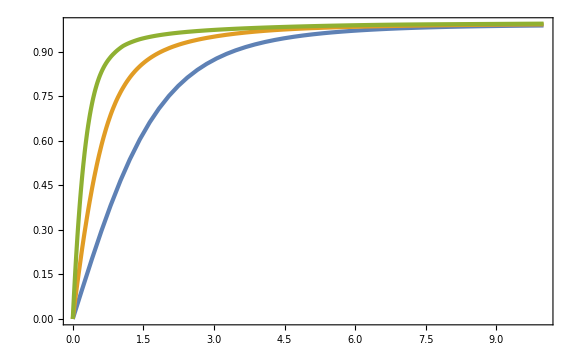

```mathematica
Plot[{Φsol[x,0],Φsol[x,5],Φsol[x,10]},{x,0,10},PlotRange->Full]
```

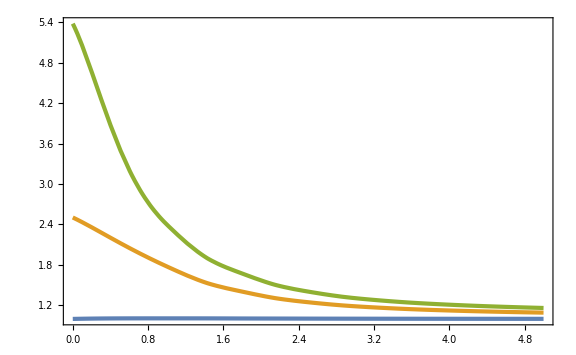

```mathematica
Plot[{Asol[x,0],Asol[x,5],Asol[x,10]},{x,0,5},PlotRange->Full]
```

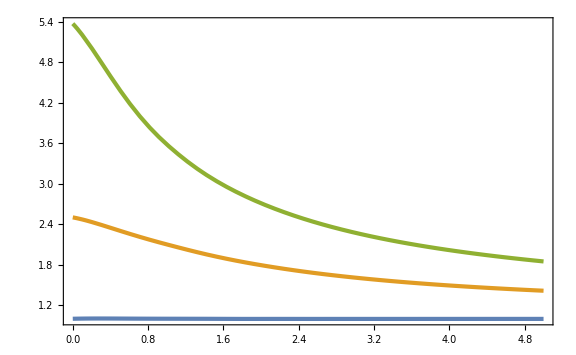

```mathematica
Plot[{Bsol[x,0],Bsol[x,5],Bsol[x,10]},{x,0,5},PlotRange->Full]
```

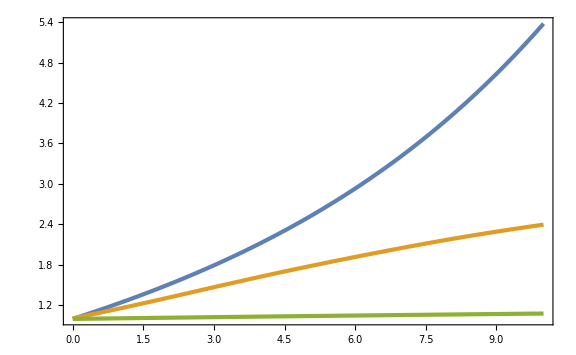

```mathematica
Plot[{Asol[0,t],Asol[1,t],Asol[10,t]},{t,0,tf}]
```

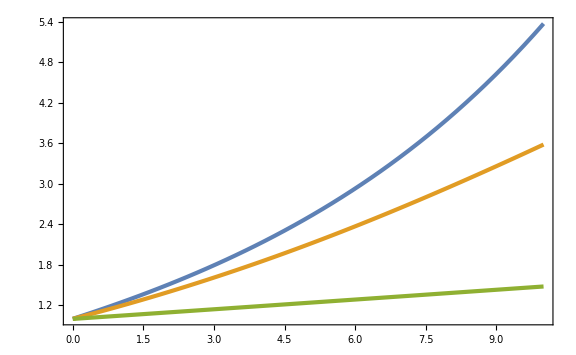

```mathematica
Plot[{Bsol[0,t],Bsol[1,t],Bsol[10,t]},{t,0,tf}]
```

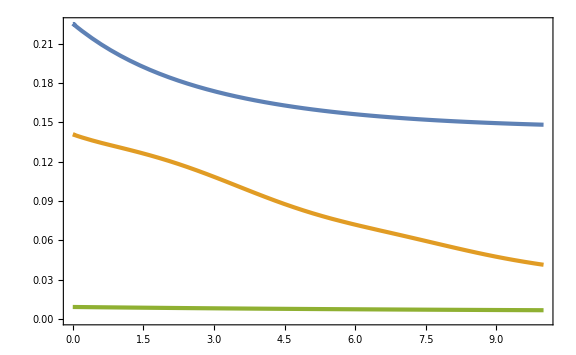

```mathematica
Plot[{HAsol[0,t],HAsol[1,t],HAsol[10,t]},{t,0,tf}]
```

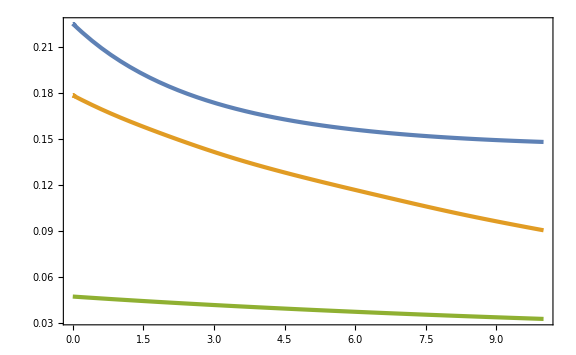

```mathematica
Plot[{HBsol[0,t],HBsol[1,t],HBsol[10,t]},{t,0,tf}]
```